```mathematica
mmax = 6;
```

```mathematica
w[x_, y_] = Amn*Sin[m*Pi*x/a]*Sin[n*Pi*y/b];
Pcr = -p/.Solve[(Derivative[4,0][w][x,y]+2*Derivative[2,2][w][x,y]+Derivative[0,4][w][x,y])-p/D*Derivative[2,0][w][x,y]==0,
p][[1]]//Simplify

Pcr1 = -p/.Solve[(Derivative[4,0][w][x,y]+2*Derivative[2,2][w][x,y]+Derivative[0,4][w][x,y])-p/D*Derivative[2,0][w][x,y]==0,
p][[1]]/.n->1//Simplify
```

(D (b^2 m^2+a^2 n^2)^2 π^2)/(a^2 b^4 m^2)

(D (a^2+b^2 m^2)^2 π^2)/(a^2 b^4 m^2)

```mathematica
k = Pcr/(Pi^2*(n^2 D)/b^2)
```

((b^2 m^2+a^2 n^2)^2)/(a^2 b^2 m^2 n^2)

```mathematica
Clear[kad]
kad[ξ_, m_, n_] = ((ξ*n)/m+m/(ξ*n))^2;
```

```mathematica
n = 1;

Solve[D[kad[ξ,m,n], ξ]==0, ξ ]
```

{{ξ→-m},{ξ→-ⅈ m},{ξ→ⅈ m},{ξ→m}}

```mathematica
kad[ξ/.Table[Solve[D[kad[ξ,m,n], ξ]==0, ξ], {m, 1, 6}][[Range[mmax]]], Range[mmax],1]
```

{{4,0,0,4},{4,0,0,4},{4,0,0,4},{4,0,0,4},{4,0,0,4},{4,0,0,4}}

```mathematica
ξcr = ξ/.Table[
Solve[kad[ξ, i,n]==kad[ξ, i+1,n], ξ,  Assumptions->ξ>0],
 {i, 1, 5}]
```

{{√2},{√6},{2 √3},{2 √5},{√30}}

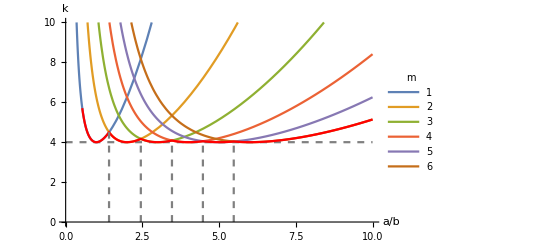

```mathematica
Show[
Plot[Evaluate[Table[kad[ξ, m,n], {m, 1, 6}]],{ξ, 0, 10}, PlotRange->{Automatic, {0, 10}}, PlotLegends->LineLegend[Range[6], LegendLabel->"m"], AxesLabel->{"a/b", "k"}
], 
Plot[4, {ξ, 0, 10}, PlotStyle->{Gray, Dashed}], 
Plot[Min[Evaluate[Table[kad[ξ, m, n], {m, 1, 6}]]],{ξ, 0, 10}, PlotStyle->{Thick, Red}],ParametricPlot[{ξcr[[1,1]],j }, {j, 0, Evaluate@kad[ξcr[[1,1]], 1,n] }, PlotStyle->{Gray, Dashed}], 
ParametricPlot[{ξcr[[2,1]],j }, {j, 0, Evaluate@kad[ξcr[[2,1]], 2,n] }, PlotStyle->{Gray, Dashed}], 
ParametricPlot[{ξcr[[3,1]],j }, {j, 0, Evaluate@kad[ξcr[[3,1]], 3,n] }, PlotStyle->{Gray, Dashed}], 
ParametricPlot[{ξcr[[4,1]],j }, {j, 0, Evaluate@kad[ξcr[[4,1]], 4,n] }, PlotStyle->{Gray, Dashed}], 
ParametricPlot[{ξcr[[5,1]],j }, {j, 0, Evaluate@kad[ξcr[[5,1]], 5,n] }, PlotStyle->{Gray, Dashed}], 
Ticks->{Evaluate[Table[ξcr[[i,1]], {i, 1, 5}]]}
]
```